```mathematica
s1[x_]:=Cos[x];
c1[x_]:=Sin[5x];
r:=Range[-10,10,.1];
c1p:=Map[c1,r];
s1p:=Map[s1,r];
```

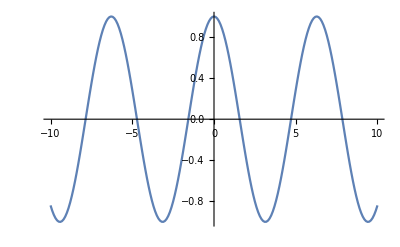

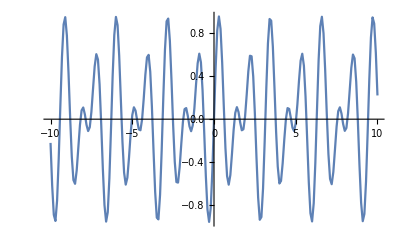

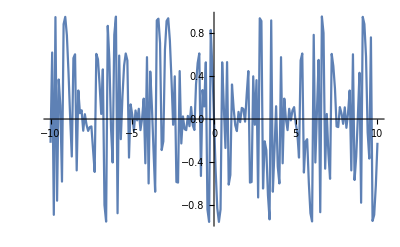

-Graphics-

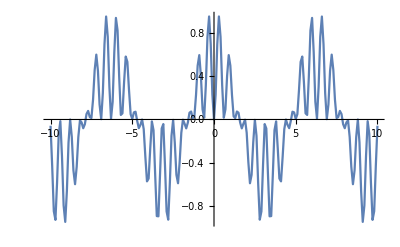

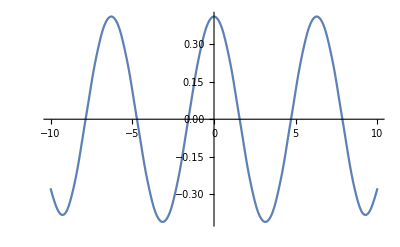

```mathematica
SeedRandom[Round[Pi*Pi]]
list:=List[]
For[i=-10,i<=10,i+=.1,
list=Append[list,If[RandomInteger[]==1,1,-1]]
]
ListLinePlot[s1p,DataRange->{-10,10}]
ListLinePlot[s1p*c1p,DataRange->{-10,10}]
res:=s1p*c1p*list
ListLinePlot[res,DataRange->{-10,10}]
ListLinePlot[res*list,DataRange->{-10,10}]
ListLinePlot[res*list*c1p,DataRange->{-10,10}]
ListLinePlot[LowpassFilter[res*list*c1p,.1],DataRange->{-10,10}]
```

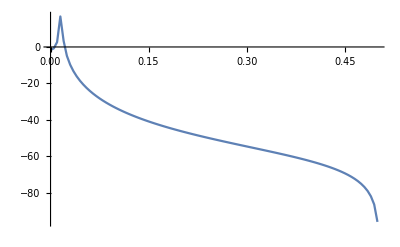

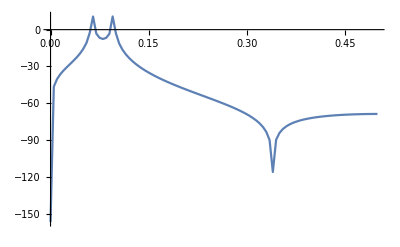

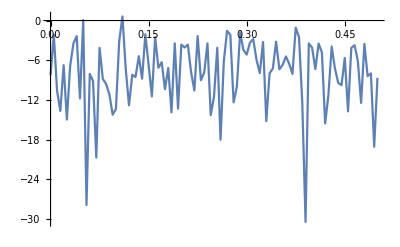

-Graphics-

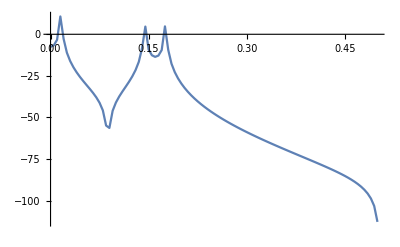

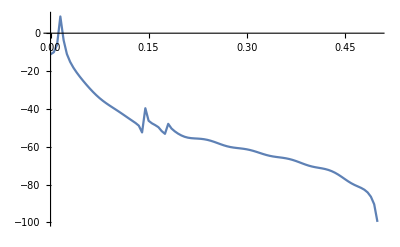

```mathematica
Periodogram[s1p]
Periodogram[s1p*c1p]
Periodogram[s1p*c1p*list]
Periodogram[s1p*c1p*list*list]
Periodogram[s1p*c1p*list*list*c1p]
Periodogram[LowpassFilter[s1p*c1p*list*list*c1p,.1]]
```